## The problem

A point mass m slides frictionless on an elliptical wire with a certain mass distribution. We are given the center-of-mass, the total mass, and the moment of inertia of the elliptical wire (or, alternatively, its mass distribution along the wire). The elliptical wire lies within a vertical plane can rotate freely around an axis around its center. It is connected to a torsional spring with constant Dspring .

## Assumptions

```mathematica
$Assumptions=$Assumptions&&a>0&&b>0 &&c>0 && Mellipse >0 && Iellipse>0&&Dspring>0&&gconst>0 &&m>0&&Element[phi[_]|th[_]|comEllipseX|comEllipseY,Reals];
```

## The Point Mass

```mathematica
(*parametrization of ellipse by _actual_ angle phi of the point w.r.t. the y-axis*)
rabs=a b/ Sqrt[(a Cos[phi[t]])^2+(b Sin[phi[t]])^2];
r = {Sin[phi[t]],-Cos[phi[t]]}*rabs;
```

```mathematica
(*rotate r by the angle th of the ellipse wrt y axis*)
rot={{Cos[th[t]],-Sin[th[t]]},{Sin[th[t]],Cos[th[t]]} };
r=rot . r // Simplify;
```

```mathematica
(*first time derivative*)
rdot= D[r,t] // Simplify;
```

```mathematica
(*second time derivative*)
rdot2=rdot[[1]]^2+rdot[[2]]^2 // Simplify;
```

```mathematica
(*kinetic energy of point mass*)
Tpoint=1/2 m rdot2;
```

```mathematica
(*gravitational potential of point mass*)
VgravPointMass=gconst*m* r[[2]];
```

## The Elliptical Wire

```mathematica
(*parametrization of ellipse - note that gam is _not_ the angle of the point on ellipse w.r.t. y-axis!*)
s = {a Sin[gam], -b Cos[gam]};
```

```mathematica
(*squared distance to center of ellipse*)
s2 = s[[1]]^2+s[[2]]^2;
```

```mathematica
(*first derivative w.r.t. parameter gam*)
sdot = D[s,gam];
```

```mathematica
(*second derivative w.r.t. parameter gam*)
sdot2 = sdot[[1]]^2+sdot[[2]]^2;
```

```mathematica
(*jacobian for line integral along ellipse*)
jac=Sqrt[sdot2];
```

```mathematica
(*kinetic energy of ellipse*)
Tellipse=1/2 Iellipse th'[t]^2;
```

```mathematica
(*potential energy of ellipse*)
VgravEllipse=gconst*Mellipse*(rot.{comEllipseX,comEllipseY})[[2]];
```

```mathematica
(*torsional spring connected to the elliptic wire*)
VspringEllipse=Dspring*(th[t]/2Pi)^2;
```

## Calculate Parameters of the Elliptical Wire from Explicit Mass Distribution

```mathematica
(*mass line density along the wire - 1/jac simplifies the integrals in the following, avoiding EllipticE functions*)
(*make sure that this integrates to Mellipse!!!*)
wireMassDens[gam_]:=Mellipse/2/Pi*(1+Cos[gam])/jac;
```

```mathematica
(*Total mass of ellipse*)
MellipseExpl = Integrate[wireMassDens[gam] jac,{gam,0,2 Pi}]
```

Mellipse

```mathematica
(*Moment of inertia of ellipse*)
IellipseExpl = Integrate[wireMassDens[gam] s2 jac,{gam,0,2 Pi}]
```

1/2 (a^2+b^2) Mellipse

```mathematica
(*center of mass times mass of ellipse*)
wireMassDens[gam] rot.s// Simplify;
comTimesMassExpl = Integrate[% *jac,{gam,-Pi,Pi}];
comExpl = comTimesMassExpl/MellipseExpl
```

{1/2 b Sin[th[t]],-1/2 b Cos[th[t]]}

```mathematica
(*potential energy of ellipse*)
VgravEllipseExpl=Mellipse*gconst*comExpl[[2]];
```

```mathematica
(*torque on ellipse computed from COM*)
τellipseExpl= Cross[Join[comTimesMassExpl,{0}],{0, gconst ,0}];
```

```mathematica
(*check: direct computation of gravitational torque*)
Cross[Join[rot.s,{0}],{0,wireMassDens[gam] gconst ,0}] // Simplify;
τellipseExplCheck= Integrate[% *jac,{gam,0,2 Pi}] // Simplify;
τellipseExpl-τellipseExplCheck
```

{0,0,0}

```mathematica
(*check: grav torque direct computation vs differentiating potential*)
D[VgravEllipse,th[t]] /. Mellipse->MellipseExpl;
τellipseExpl[[3]];
```

```mathematica
(*put these results into a rule*)
valsExplMassDist={Iellipse->IellipseExpl,comEllipseX->comExpl[[1]]/.th[t]->0,comEllipseY->comExpl[[2]]/.th[t]->0};
```

```mathematica
(*from these values, build numerical test case*)
testvalsNoMellipse={a->1,b->2,m->1,Dspring->0,gconst->10};
testvalsNoMellipse=Join[testvalsNoMellipse,valsExplMassDist/.testvalsNoMellipse];
testvals=Join[testvalsNoMellipse/.Mellipse->1,{Mellipse->1}]
```

{a→1,b→2,m→1,Dspring→0,gconst→10,Iellipse→5/2,comEllipseX→0,comEllipseY→-1,Mellipse→1}

## Investigate the Gravitational Potential for Minima (setting Dspring=0)

```mathematica
(*insert the elxplicit parameters from above into the grav potential*)
VstabTest=(VgravPointMass+VgravEllipse) /. valsExplMassDist /.{phi[t]->phi, th[t]->th} // Simplify;
```

{-5 Cos[th]-(20 Cos[phi+th])/(√(Cos[phi]^2+4 Sin[phi]^2))}

-Graphics3D-

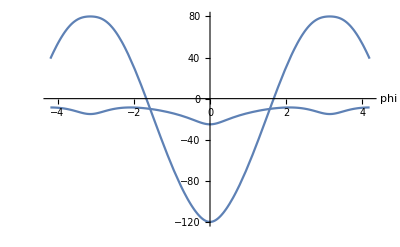

```mathematica
(*from the plot we can see that there are potential minima at phi=-th=±Pi, depending on the value of Mellipse*)
func=VstabTest  /. Mellipse->{1/2}/. testvalsNoMellipse
surf=Plot3D[func,{phi,-Pi/3-Pi,Pi+Pi/3},{th,-Pi-Pi/3,Pi+Pi/3},AxesLabel->{"phi","th"}];
(*line along phi=-th*)
line=ParametricPlot3D[{phi,-phi,func/.th->-phi},{phi,-Pi/3-Pi,Pi+Pi/3},PlotStyle->{Red,Thick}];
(*box around ±π*)
lineBox1=ParametricPlot3D[{phi,-Pi,func/.th->-Pi},{phi,-Pi/3-Pi,Pi+Pi/3},PlotStyle->{Green,Thick}];
lineBox2=ParametricPlot3D[{phi,Pi,func/.th->Pi},{phi,-Pi/3-Pi,Pi+Pi/3},PlotStyle->{Green,Thick}];
lineBox3=ParametricPlot3D[{-Pi,th,func/.phi->-Pi},{th,-Pi/3-Pi,Pi+Pi/3},PlotStyle->{Green,Thick}];lineBox4=ParametricPlot3D[{Pi,th,func/.phi->Pi},{th,-Pi/3-Pi,Pi+Pi/3},PlotStyle->{Green,Thick}];
(*3d plot*)
Show[surf,line,lineBox1,lineBox2,lineBox3,lineBox4]
(*2d plot along diagonal*)
Plot[VstabTest  /. th->-phi /. Mellipse->{1/2,10}/. testvalsNoMellipse,{phi,-Pi/3-Pi,Pi+Pi/3},AxesLabel->{"phi"}]
```

```mathematica
(*Analyse potential extremum at phi=-th=±Pi*)
```

```mathematica
(*Evaluate the first derivatives -> zero*)
D[VstabTest,phi]/.{phi->-Pi,th->Pi} 
D[VstabTest,th]/.{phi->-Pi,th->Pi}
```

0

0

```mathematica
(*Compute second derivatives*)
DphiDphi=D[D[VstabTest,phi],phi]/.{phi->-Pi,th->Pi}  // Simplify;
DphiDth=D[D[VstabTest,phi],th]/.{phi->-Pi,th->Pi} //Simplify;
DthDth=D[D[VstabTest,th],th]/.{phi->-Pi,th->Pi}  // Simplify;
```

```mathematica
(*Compute Hessian determionant: is linear in Mellipse with negative gradient. For a>b, the det is always negative -> no extremum. For b>a, the det changes sign from + to - at a certain value of Mellipse. Below this value -> has extremum. Above this value -> no extremum*)
detHess=DphiDphi*DthDth-DphiDth^2 ;
detHess=Collect[detHess,Mellipse,Simplify]
critMellipse=Solve[detHess==0,{Mellipse}]
```

(b^2 (-a^2+b^2) gconst^2 m^2)/a^2-(b^4 gconst^2 m Mellipse)/(2 a^2)

{{Mellipse→ConditionalExpression[-(2 a^2 b^2 gconst^2 m^2-2 b^4 gconst^2 m^2)/(b^4 gconst^2 m), a<b]}}

```mathematica
(*the second derivative in phi is positive -> We got a local minimum.*)
DphiDphi /. critMellipse
```

{(b^3 gconst m)/a^2}

```mathematica
(*numerical value for critical Mellipse for our numerical test input*)
critMellipse[[1,1]] /. testvalsNoMellipse
```

Mellipse→3/2

## The Exact Euler-Lagrange Equations (ELEs)

```mathematica
(*the Lagrangian*)
Vtot=VspringEllipse+VgravPointMass+VgravEllipse;
Ttot=Tpoint+Tellipse;
L=Ttot-Vtot;
```

```mathematica
(*derivatives by the angles*)
dLdPhi=D[L,phi[t]] // Simplify;
dLdTh=D[L,th[t]] // Simplify;
```

```mathematica
(*derivatives by the angular velocities*)
dLdPhiDot=D[L,D[phi[t],t]] // Simplify;
dLdThDot=D[L,D[th[t],t]] // Simplify;
(*time derivatives of the derivatives by the angular velocities*)
D[dLdPhiDot,t] // Simplify;
D[dLdThDot,t] // Simplify;
```

```mathematica
(*the two coupled ELEs*)
ele1=(dLdPhi == D[dLdPhiDot,t])//Simplify;
ele2=(dLdTh == D[dLdThDot,t])//Simplify;
```

## A Special Case: The Circle

```mathematica
(*taking the difference of the ELEs reveals th``=0*)
(dLdTh-dLdPhi == D[dLdThDot,t]-D[dLdPhiDot,t]) /. {a->R,b->R,Dspring->0,comEllipseX->0,comEllipseY->0} // Simplify
```

th''[t]==0

```mathematica
(*plugging this into the first ELE yields phi``=0*)
(dLdPhi == D[dLdPhiDot,t])/. {a->R,b->R,Dspring->0,comEllipseX->0,comEllipseY->0} /. D[D[th[t],t],t]->0 //Simplify
```

gconst √(R^2) Sin[phi[t]+th[t]]+R^2 phi''[t]==0

This means that the bead just moves around the circle with constant speed and the circle keeps rotating with the same angular velocity around its center. There is no coupling between the bead and the circle because the centripetal force always points towards the center of circle, meaning that it does not transfer work.

## The ELEs in Small Angle Approximation

```mathematica
(*As discussed above, there may be 2 stable points. Decide which one we want to analyze. Note: For phi=Pi, Dspring!=0 causes inhomogenous ODE.*)
whichStablePoint="0";
angShiftRu=Switch[whichStablePoint,
"0",{},
"0-Dspring0",{Dspring->0},
 "Pi-Dspring0",{phi[t]->phi[t]-π,th[t]->th[t]-π,Dspring->0},
_,{}
];
```

```mathematica
(*rescale phi and th homogenously for the order count.*)
rescaleRuξ={phi[t_] -> ξ phi[t] ,th[t_] -> ξ th[t], Derivative[n_][phi][t_] -> ξ Derivative[n][phi][t], Derivative[n_][th][t_] -> ξ Derivative[n][th][t]};
```

```mathematica
(*expand the eles in ξ*)
{ele1,ele2}  /.angShiftRu /. rescaleRuξ ;
Simplify[Normal[Series[#,{ξ,0,1}]]]& /@ %;
{ele1approx,ele2approx}=%/. ξ->1;
ele1approx
ele2approx
```

b^2 gconst phi[t]+a^2 (gconst th[t]+b (phi''[t]+th''[t]))==0

gconst (comEllipseY Mellipse th[t]-b m (phi[t]+th[t]))==comEllipseX gconst Mellipse+1/2 Dspring π^2 th[t]+b^2 m phi''[t]+(Iellipse+b^2 m) th''[t]

```mathematica
(*Note that comEllipseX!=0 renders the eles inhomogenous. The small-angle approximation inherently assumes that comEllipseX is small, otherwise the system would quickly acquire a large angle th because the elliptical wire will tip over.*)
{ele1approx,ele2approx}={ele1approx,ele2approx}/.comEllipseX->0
```

{b^2 gconst phi[t]+a^2 (gconst th[t]+b (phi''[t]+th''[t]))==0,gconst (comEllipseY Mellipse th[t]-b m (phi[t]+th[t]))==1/2 Dspring π^2 th[t]+b^2 m phi''[t]+(Iellipse+b^2 m) th''[t]}

## Solving the ELEs in Small Angle Approximation

```mathematica
(*obtain an exact solution of the approximate eles using Mathematica's DSolve*)
exactsolapprox=DSolve[{ele1approx,ele2approx,phi'[0]==1,th'[0]==0,phi[0]==0,th[0]==0},{phi[t],th[t]},t];
exactsolapprox[[1,1]] /. testvals //N;
exactsolapprox[[1,2]] /. testvals //N;
(*check initial conditions*)
{phi[t],th[t]} /. exactsolapprox /. t->0;
D[#,t]& /@({phi[t],th[t]}/.exactsolapprox)/. t->0 // Simplify
```

{{1,0}}

```mathematica
(*Alternatively, obtain a system of equations in the form y''[t]=M.y[t]*)
eleApproxSyst=Simplify /@ Solve[ele1approx&&ele2approx,{phi''[t],th''[t]}];
(*extract the matrix M*)
eleApproxMat= {
{Coefficient[phi''[t]/.eleApproxSyst,phi[t]][[1]],
Coefficient[phi''[t]/.eleApproxSyst,th[t]][[1]]},
{Coefficient[th''[t]/.eleApproxSyst,phi[t]][[1]],
Coefficient[th''[t]/.eleApproxSyst,th[t]][[1]]}};
(*check*)
eleApproxMat.{phi[t],th[t]};
{phi''[t],th''[t]} /. eleApproxSyst[[1]] ;
%-%% // Simplify
```

{0,0}

```mathematica
(*the solution to the eles is obtained by computing the eigensystem*)
eleApproxMatES = Eigensystem[eleApproxMat] //Simplify;
% /. testvalsNoMellipse// Simplify;
(*the square roots of the eigenvalues are the frequencies of the normal modes*)
eigenvals=Sqrt /@ %[[1]] // Simplify
(*the entries of the EV correspond to the coefficients of the exponentials in phi(t) and th(t). because the entries for the first normal mode have opposite signs, phi and th are out of phase in this mode*)
eigenvecs=%%[[2]] // Simplify
```

{√2 √(-(6+6 Mellipse+√(36+42 Mellipse+16 Mellipse^2))/Mellipse),√2 √((-6-6 Mellipse+√(36+42 Mellipse+16 Mellipse^2))/Mellipse)}

{{1/12 (-6-4 Mellipse-√(36+42 Mellipse+16 Mellipse^2)),1},{1/12 (-6-4 Mellipse+√(36+42 Mellipse+16 Mellipse^2)),1}}

```mathematica
(*for choice Mellipse=1*)
eigenvals /. Mellipse->1 // Simplify // N
eigenvecs /. Mellipse->1 // Simplify // N
```

{0.+6.58716 ⅈ,0.+2.14692 ⅈ}

{{-1.64128,1.},{-0.0253867,1.}}

```mathematica
(*the complex solutions*)
phisol[t_]:=A  eleApproxMatES [[2,1,1]] Exp[I Sqrt[-eleApproxMatES[[1,1]]]t]+B eleApproxMatES [[2,2,1]] Exp[I Sqrt[-eleApproxMatES[[1,2]]]t];
thsol[t_]:=A  eleApproxMatES [[2,1,2]] Exp[I Sqrt[-eleApproxMatES[[1,1]]]t]+B  eleApproxMatES [[2,2,2]] Exp[I Sqrt[-eleApproxMatES[[1,2]]]t];
(*the physical solutions are the real parts thereof - the following manipulations assume that the exponents are imaginary!*)
phisolre[t_]:=(phisol[t]+(phisol[t]/.{A->Conjugate[A],B->Conjugate[B],Exp[a_]->Exp[-a]}))/2;
thsolre[t_]:=(thsol[t]+(thsol[t]/.{A->Conjugate[A],B->Conjugate[B],Exp[a_]->Exp[-a]}))/2;
```

```mathematica
(*the real and complex parts for the coefficitents A,B are obtained from bdy conditions for phi/th and phi'/th', respectively*)
NSolve[(phisol[0]==0 && thsol[0]==0 ),{A,B}][[1]];
NSolve[(phisol'[0]==1 && thsol'[0]==0 ),{A,B}][[1]];
(*thus, the final coefficients can be obtained as the sum (of real and complex parts)*)
({A,B}/.%%) + ({A,B}/.%);
coeffs={A->%[[1]],B->%[[2]]};
% /.testvals
```

{A→0.+0.0939483 ⅈ,B→0.-0.288251 ⅈ}

```mathematica
(*compare manual solution against automatic mathematica solution*)
(phisolre[t]-exactsolapprox[[1,1,2]])/.coeffs/.testvals /. t->RandomInteger[10000]/10000//Simplify  // If[Abs[#]<1*^-15,0,#]&
(thsolre[t]-exactsolapprox[[1,2,2]])/.coeffs/.testvals  /. t->RandomInteger[10000]/10000//Simplify // If[Abs[#]<1*^-15,0,#]&
```

0

0

```mathematica
(*what IC do I need to get the pure first and second normal modes? (A=0 and B=0, respectively)*)
getIC[Aval_,Bval_]:={phisolre[0],thsolre[0],phisolre'[0],thsolre'[0]} /.{A->Aval,B->Bval}
getIC[0,1*^-3]/. testvals// N
getIC[1*^-3,0]/. testvals// N
```

{-0.0000253867,0.001,0.,0.}

{-0.00164128,0.001,0.,0.}

## Set Explicit Values for Variables and Initial Conditions

### Consistency considerations for values of moment of inertia

Note : For consistency, we need
	Mellipse Min[a,b]^2 < Iellipse < Mellipse Max[a,b]^2
and, because I = I_COM + r_COM^2 Mellipse  and I_COM > 0
	Mellipse (comEllipseX^2 + comEllipseY^2) < Iellipse
so that, in total,
	Mellipse Max[Min[a,b]^2,comEllipseX^2 + comEllipseY^2] < Iellipse < Mellipse Max[a,b]^2

```mathematica
(*take these constraints into consideration by constructing Iellipse from Mellipse, a, b, and comEllipseX/Y*)
IellipseConstr=Mellipse*(Max[Min[a,b]^2,comEllipseX^2+comEllipseY^2]+Max[a,b]^2)/2
```

1/2 Mellipse (Max[a,b]^2+Max[comEllipseX^2+comEllipseY^2,Min[a,b]^2])

### No gravity

```mathematica
(*no grav, no spring, no offset COM*)
valsNoGravSpringOffset={a->1,b->2,m->1,Dspring->0,gconst->0,Mellipse->1,comEllipseX->0,comEllipseY->0};
valsNoGravSpringOffset=Join[valsNoGravSpringOffset,{Iellipse->IellipseConstr/.valsNoGravSpringOffset}];
iniNoGravSpringOffset=(phi[0]==0&&th[0]==0 && phi'[0]==1&&th'[0]==0);
```

```mathematica
(*no grav, no spring, no offset COM, heavy point mass, light wire*)
valsNoGravSpringOffsetHeavyPoint={a->1,b->2,m->100,Dspring->0,gconst->10,Mellipse->1/100,comEllipseX->0,comEllipseY->0};
valsNoGravSpringOffsetHeavyPoint=Join[valsNoGravSpringOffsetHeavyPoint,{Iellipse->IellipseConstr/.valsNoGravSpringOffsetHeavyPoint}];
iniNoGravSpringOffsetHeavyPoint=(phi[0]==-Pi/4&&th[0]==+Pi/4 &&  phi'[0]==0&&th'[0]==0);
```

```mathematica
(*no grav, no spring, no offset COM, light point mass, heavy wire*)
valsNoGravSpringOffsetLightPoint={a->1,b->2,m->1/100,Dspring->0,gconst->10,Mellipse->100,comEllipseX->0,comEllipseY->0};
valsNoGravSpringOffsetLightPoint=Join[valsNoGravSpringOffsetLightPoint,{Iellipse->IellipseConstr/.valsNoGravSpringOffsetLightPoint}];
iniNoGravSpringOffsetLightPoint=(phi[0]==Pi/4&&th[0]==0 && phi'[0]==0&&th'[0]==0);
```

```mathematica
(*no grav and offset COM, but spring*)
valsSpring={a->1,b->2,m->1,Dspring->1,gconst->0,Mellipse->1,comEllipseX->0,comEllipseY->0};
valsSpring=Join[valsSpring,{Iellipse->IellipseConstr/.valsSpring}];
iniSpring=(phi[0]==0&&th[0]==0 && phi'[0]==1&&th'[0]==0);
```

### General Case: Gravity, Spring, and offset COM

```mathematica
(*grav, spring, offset COM*)
valsGeneral={a->1,b->2,m->1,Dspring->1,gconst->10,Mellipse->1,comEllipseX->1/2,comEllipseY->0};
valsGeneral=Join[valsGeneral,{Iellipse->IellipseConstr/.valsGeneral}];
iniGeneral=(phi[0]==-Pi/4&&th[0]==+Pi/4 && phi'[0]==0&&th'[0]==0);
```

### Small-Angle Approximation and Normal Modes

```mathematica
(*small angle approximation valid, with grav, spring, and offset COM*)
(*note that we assume comEllipseX=0 in the small-angle approximation*)
valsSmallAngle={a->1,b->2,m->1,Dspring->1,gconst->10,Mellipse->1,comEllipseX->0,comEllipseY->1};
valsSmallAngle=Join[valsSmallAngle,{Iellipse->IellipseConstr/.valsSmallAngle}];
iniSmallAngle=(phi[0]==-Pi/100&&th[0]==0 && phi'[0]==0&&th'[0]==0);
```

```mathematica
(*see above: IC for the first normal mode*)
(*note that we assume comEllipseX=0 in the small-angle approximation*)
valsSmallAngleN1={a->1,b->5,m->1,Dspring->0,gconst->10,Mellipse->1,comEllipseX->0,comEllipseY->0};
valsSmallAngleN1=Join[valsSmallAngleN1,{Iellipse->IellipseConstr/.valsSmallAngleN1}];
getIC[0,1*^-1]/.valsSmallAngleN1
(*stable point phi=0, theta=0*)
iniSmallAngleN1phi0=(phi[0]==%[[1]]&&th[0]==%[[2]] && phi'[0]==%[[3]]&&th'[0]==%[[4]]);
(*stable point phi=Pi,theta=-Pi*)
iniSmallAngleN1phiPi=(phi[0]==%%[[1]]+Pi&&th[0]==%%[[2]]-Pi && phi'[0]==%%[[3]]&&th'[0]==%%[[4]]);
```

{(-3700+140 √673)/48000,1/10,0,0}

```mathematica
(*see above: IC for the second normal mode*)
(*note that we assume comEllipseX=0 in the small-angle approximation*)
valsSmallAngleN2={a->1,b->3,m->1,Dspring->0,gconst->10,Mellipse->1,comEllipseX->0,comEllipseY->0};
valsSmallAngleN2=Join[valsSmallAngleN2,{Iellipse->IellipseConstr/.valsSmallAngleN2}];
getIC[1*^-1,0]/.valsSmallAngleN2
(*stable point phi=0, theta=0*)
iniSmallAngleN2phi0=(phi[0]==%[[1]]&&th[0]==%[[2]] && phi'[0]==%[[3]]&&th'[0]==%[[4]]);
(*stable point phi=Pi,theta=-Pi*)
iniSmallAngleN2phiPi=(phi[0]==%%[[1]]+Pi&&th[0]==%%[[2]]-Pi && phi'[0]==%%[[3]]&&th'[0]==%%[[4]]);
```

{(-780-20 √1361)/9600,1/10,0,0}

### Analysis of second (meta) stable point -ϕ=θ=π

```mathematica
(*Stability analysis*)
stable=+1 (*set to +1 for stable, -1 for unstable*)
valsStab={a->1,b->5,m->1,Dspring->0,gconst->10,comEllipseX->0};
(*find critical Mellipse*)
critMellipseExplStab=Mellipse /. critMellipse[[1]] /. valsStab
valsStab=Join[valsStab,{Mellipse->critMellipseExplStab-stable/10}];
valsStab=Join[valsStab,{Iellipse->1/2(a^2+b^2)Mellipse,comEllipseY->-b/2}/.valsStab];
iniStab=(phi[0]==-Pi&&th[0]==+Pi+1/100&& phi'[0]==0&&th'[0]==0);
```

1

48/25